```mathematica
(* BLOCK 1 - Definitions and initializations *)

Clear[a];

(* Assume all variables are real *)
$Assumptions=Element[x0[τ],Reals]&&Element[x1[τ],Reals]&&Element[x2[τ],Reals]&&Element[x3[τ],Reals]&&Element[p0[τ],Reals]&&Element[p1[τ],Reals]&&Element[p2[τ],Reals]&&Element[p3[τ],Reals]&&Element[s,Reals]&&x1[τ]>2M&&Element[a,Reals]&&0<x2[τ]<π;

(* Coordinates *)

(* X^μ *)
X={x0[τ],x1[τ],x2[τ],x3[τ]};

(* Subscript[P, μ] *)
P={p0[τ],p1[τ],p2[τ],p3[τ]};

(* Subscript[P, i] *)
p={p1[τ],p2[τ],p3[τ]};


(* BL coordinates in Kerr (t, r, θ, ϕ) = (x0, x1, x2, x3) *)

M=1;  (* mass *)
rs = 2M; (* Schwarzschild radius *)

Σ=r^2+a^2 Cos[θ]^2/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
Δ=r^2-rs r+a^2/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
A=(r^2+a^2)^2-a^2 Δ Sin[θ]^2/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];

(* Metric Subscript[g, μν] *)

g=({{-(1-(rs r)/Σ), 0, 0, -(rs a r Sin[θ]^2)/Σ}, {0, Σ/Δ, 0, 0}, {0, 0, Σ, 0}, {-(rs a r Sin[θ]^2)/Σ, 0, 0, A Sin[θ]^2/Σ}})/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];

(* Inverse metric g^μν *)

ig=Inverse[g]//Simplify;

(* Orthonormal tetrad (Subscript[e, a])^μ and dual tetrad Subscript[(d^a), μ], with (Subscript[e, a])^μ = t^μ *)

e0={(r^2+a^2)/(√(Σ Δ)),0,0,a/(√(Σ Δ))}/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
e1={0,√(Δ/Σ),0,0}/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
e2={0,0,√(1/Σ),0}/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
e3={(a Sin[θ]^2)/(√Σ Sin[θ]),0,0,1/(√Σ Sin[θ])}/.r->x1[τ]/.θ->x2[τ]/.ϕ->x3[τ];
d0=(e0.g)//Simplify;
d1=(e1.g)//Simplify;
d2=(e2.g)//Simplify;
d3=(e3.g)//Simplify; 
T=e0;
Td=d0;

Detg=Det[g]//Simplify;

(* Christoffel Subscript[Γ^i, jk] = 1/2 g^im( ∂_k Subscript[g, mj] + ∂_j Subscript[g, mk] - ∂_m Subscript[g, jk] ) *)

Γ=1/2 Parallelize[Table[(∑_(m=1)^4 (ig[[i]][[m]](D[g[[m]][[j]],X[[k]]]+D[g[[m]][[k]],X[[j]]]-D[g[[j]][[k]],X[[m]]])))//Simplify,{i,1,4},{j,1,4},{k,1,4}]];

(* Riemann Subscript[R^i, jkl] = ∂_k Subscript[Γ^i, lj] - ∂_l Subscript[Γ^i, kj] + Subscript[Γ^i, km] Subscript[Γ^m, lj] - Subscript[Γ^i, lm] Subscript[Γ^m, kj] *)

Riem=Table[(D[Γ[[i]][[l]][[j]],X[[k]]]-D[Γ[[i]][[k]][[j]],X[[l]]]+∑_(m=1)^4 (Γ[[i]][[k]][[m]]Γ[[m]][[l]][[j]]-Γ[[i]][[l]][[m]]Γ[[m]][[k]][[j]]))//Simplify,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Parallelize;

(* Riemann Subscript[R, ijkl] *)
R=Table[∑_(i1=1)^4 g[[i1]][[i]]Riem[[i1]][[j]][[k]][[l]]//Simplify,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Parallelize;

(* P^μ = g^μα Subscript[P, α] *)

Pu=Table[(∑_(α=1)^4 (ig[[μ]][[α]]P[[α]]))//Simplify,{μ,1,4}]//Parallelize;

(* H = 1/2 g^μν Subscript[P, μ] Subscript[P, ν] = 0  =>  Subscript[P, 0] = 1/g^00(-g^(0i)Subscript[P, i] + √((g^(0i)Subscript[P, i])^2 - g^00 g^ij Subscript[P, i] Subscript[P, j])) *)
pt0=(ig[[1]][[1]])^-1(-(∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))+((∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))^2-ig[[1]][[1]](∑_(i=2)^4 ∑_(j=2)^4 (ig[[i]][[j]]P[[i]]P[[j]])))^(1/2))//Simplify;


(* Spin tensor Subscript[S, αβ] = -s/(T^μ Subscript[P, μ])Subscript[ϵ, αβγδ] P^γ T^δ *)

S=Parallelize[Table[-s/(T.P)Sqrt[-Detg]*∑_(γ=1)^4 ∑_(δ=1)^4 LeviCivitaTensor[4][[α]][[β]][[γ]][[δ]]Pu[[γ]]T[[δ]]//FullSimplify,{α,1,4},{β,1,4}]]//FullSimplify; 
Su=Table[∑_(γ=1)^4 ∑_(δ=1)^4 S[[γ]][[δ]]ig[[γ]][[α]]ig[[δ]][[β]]//FullSimplify,{α,1,4},{β,1,4}]//Parallelize//FullSimplify;

(* ∇_μ Subscript[T, α] = ∂_μ Subscript[T, α] - Subscript[Γ^ρ, μα] Subscript[T, ρ] *)
DTd=Table[(D[Td[[α]],X[[μ]]]-∑_(ρ=1)^4 (Γ[[ρ]][[μ]][[α]]Td[[ρ]]))//FullSimplify,{μ,1,4},{α,1,4}]//Parallelize;
(* P^μ∇_μ Subscript[T, α] = P^μ(∂_μ Subscript[T, α] - Subscript[Γ^ρ, μα] Subscript[T, ρ]) *)
PDTd=Table[(∑_(μ=1)^4 Pu[[μ]]DTd[[μ]][[α]])//FullSimplify,{α,1,4}]//Parallelize;
(* ϵ/(T^ρ Subscript[P, ρ])S^μα P^ν∇_ν Subscript[T, α] *)
dx1=Parallelize[Table[ϵ/(T.P)(∑_(α=1)^4 Su[[μ]][[α]]PDTd[[α]])//Simplify,{μ,1,4}]];
(* Subscript[Γ^α, βμ] Subscript[P, α](ẋ)^β *)

Pd=Table[(∑_(α=1)^4 ∑_(β=1)^4 (Γ[[α]][[β]][[μ]]P[[α]](Pu[[β]]+dx1[[β]])))//Simplify,{μ,1,4}]//Parallelize;
RS=Parallelize[Table[ϵ/2∑_(i=1)^4 ∑_(j=1)^4 ∑_(k=1)^4 Pu[[i]]Su[[j]][[k]]R[[j]][[k]][[α]][[i]]//Simplify,{α,1,4}]];
pd=Table[Pd[[i]],{i,2,4}];
Rs=Table[RS[[i]],{i,2,4}];

EOM={D[X,τ]==Pu+dx1,D[p,τ]==pd-Rs}/.p0[τ]->pt0;
```

-Graphics3D-

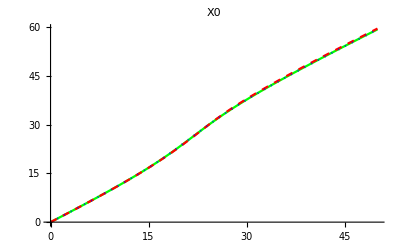

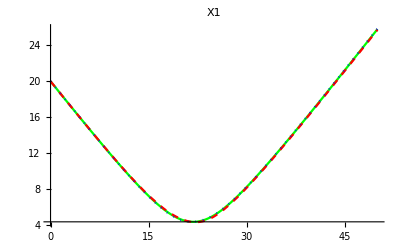

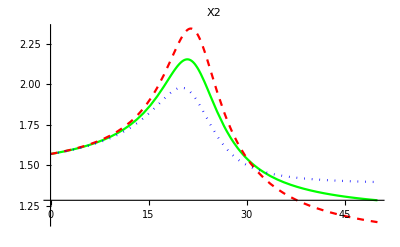

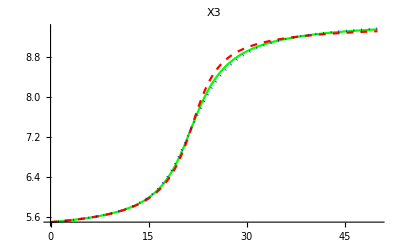

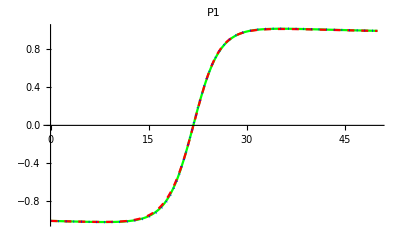

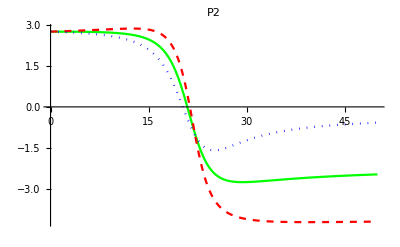

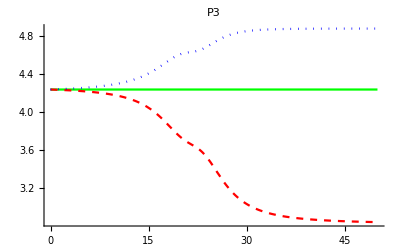

```mathematica
(* Trajectories *)

Clear[a,s,ϵ];

(* EOM *)

EOM0=EOM/.s->0;
EOM1=EOM/.s->-s;
EOM2=EOM;

(* Initial conditions *)
(* integration time τmax, small parameter/wavelength ϵ, Kerr parameter a  *)
τ0=0;
τmax=5 10^1;
ϵ=20 10^-1;
a=0.99;

(* spin/polarization *)
s=1;

(* initial position *)
x0i=0;
x1i=10rs;
x2i=π/2;
x3i=π/2+π/4+π;

(* initial normalized momentum Pid *)
ψ=π/(24/10);
ρ=π/2.2;
Pid=(-d0+Sin[ψ]Sin[ρ]d1+Sin[ψ]Cos[ρ]d2+Cos[ψ]d3);
p1i=-Pid[[2]]/.τ->τ0;
p2i=Pid[[3]]/.τ->τ0;
p3i=Pid[[4]]/.τ->τ0;

(* initial data vector *)
id=(X/.τ->τ0)=={x0i,x1i,x2i,x3i}&&(p/.τ->τ0)=={p1i,p2i,p3i};

(* stop if integration hits event horizon x1 = 2rs *)
τint0=τmax;
horizon0=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint0=τ}];
τint1=τmax;
horizon1=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint1=τ}];
τint2=τmax;
horizon2=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint2=τ}];

(* Integration *)

sol0=NDSolve[EOM0&&id&&horizon0,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax}];
sol1=NDSolve[EOM1&&id&&horizon1,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax}];
sol2=NDSolve[EOM2&&id&&horizon2,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax}];



(* Plots *)

(* Plot range *)
range=10rs;
τplot0=Min[τint0,τmax];
τplot1=Min[τint1,τmax];
τplot2=Min[τint2,τmax];

(* 3D Plot *)
arrow1={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range+range/4,-0.9range,0}},0.2],-0]};
arrow2={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range,-0.9range+range/4,0}},0.2],-0]};
arrow3={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range,-0.9range,range/4}},0.2],-0]};
arrowtext1=Text[Style["x",Large,Bold],{-0.9range+range/3.5,-0.9range,0}];
arrowtext2=Text[Style["y",Large,Bold],{-0.9range,-0.9range+range/3.5,0}];
arrowtext3=Text[Style["z",Large,Bold],{-0.9range,-0.9range,range/3.5}];
frame=Graphics3D[{Yellow,arrow1,arrow2,arrow3,Black,arrowtext1,arrowtext2,arrowtext3}];
wall1=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,-range,-range},{-range,range,-range},{range,range,-range},{range,-range,-range}}]}];
wall2=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,range,-range},{-range,-range,-range},{-range,-range,range},{-range,range,range}}]}];
wall3=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,-range,-range},{-range,-range,range},{range,-range,range},{range,-range,-range}}]}];
source=Graphics3D[{Specularity[White,5],Orange,Sphere[{x1i Sin[x2i]Cos[x3i],x1i Sin[x2i]Sin[x3i],x1i Cos[x2i]},0.3rs]}];
plane=ContourPlot3D[z==0,{x,-range,range},{y,-range,range},{z,-range,range},Mesh->None,ContourStyle->Opacity[0.5]];
BH=Graphics3D[{Specularity[White,3],Black,Sphere[{0,0,0},M+√(M^2-a^2)]}];

g0=ParametricPlot3D[{Evaluate[(x1[τ]Sin[x2[τ]]Cos[x3[τ]])/.sol0][[1]],Evaluate[(x1[τ]Sin[x2[τ]]Sin[x3[τ]])/.sol0][[1]],Evaluate[(x1[τ]Cos[x2[τ]])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->{Thick,Green},PlotPoints->3000];
g1=ParametricPlot3D[{Evaluate[(x1[τ]Sin[x2[τ]]Cos[x3[τ]])/.sol1][[1]],Evaluate[(x1[τ]Sin[x2[τ]]Sin[x3[τ]])/.sol1][[1]],Evaluate[(x1[τ]Cos[x2[τ]])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Thick,Red},PlotPoints->3000];
g2=ParametricPlot3D[{Evaluate[(x1[τ]Sin[x2[τ]]Cos[x3[τ]])/.sol2][[1]],Evaluate[(x1[τ]Sin[x2[τ]]Sin[x3[τ]])/.sol2][[1]],Evaluate[(x1[τ]Cos[x2[τ]])/.sol2][[1]]},{τ,0,τplot2},PlotStyle->{Thick,Blue},PlotPoints->3000];

Style[Show[g0,g1,g2,BH,source,plane,wall1,wall2,wall3,frame,PlotRange->{{-range,range},{-range,range},{-range,range}},Boxed->False,Axes->False,ViewPoint->{1.5,4,1.5}],Antialiasing->True]

(* Individual Plots *)

Show[Plot[{Evaluate[(x0[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All],Plot[{Evaluate[(x0[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All],Plot[{Evaluate[(x0[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All]]

Show[Plot[{Evaluate[(x1[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All],Plot[{Evaluate[(x1[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All],Plot[{Evaluate[(x1[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All]]

Show[Plot[{Evaluate[(x2[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All],Plot[{Evaluate[(x2[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All],Plot[{Evaluate[(x2[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All]]

Show[Plot[{Evaluate[(x3[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(x3[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(x3[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All]]

Show[Plot[{Evaluate[(p1[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All],Plot[{Evaluate[(p1[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All],Plot[{Evaluate[(p1[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All]]

Show[Plot[{Evaluate[(p2[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All],Plot[{Evaluate[(p2[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All],Plot[{Evaluate[(p2[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All]]

Show[Plot[{Evaluate[(p3[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All],Plot[{Evaluate[(p3[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All],Plot[{Evaluate[(p3[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All]]
```